## Define flow and import package

```mathematica
SetDirectory[NotebookDirectory[]]
<<lagrange2d.wl;
RandomSeed[0];
(*params = {A->0.1,ϵ->0.25,ω->π/5};*)
```

/Users/william/program_repos/lagrange2d

```mathematica
a[t_]:=ϵ Sin[ω t];
b[t_]:=1-2 ϵ Sin[ω t];
f[t_,x_]:=a[t] x^2+b[t] x;

g[t_,x_,y_]:=π A Sin[π f[t,x]]Cos[π f[t,y]](*D[f[t,x],x]*)

(* quad gyre *)
{vx[t_,x_,y_],vy[t_,x_,y_]}:={g[t,x,y],-g[t,y,x](2 a[t] x+b[t])};

(* double gyre *)
{vx[t_,x_,y_],vy[t_,x_,y_]}:={-π A Sin[π f[t,x]]Cos[π y],π A Cos[π f[t,x]]Sin[π y](2 a[t] x+b[t])};

params = {A->0.1,ϵ->0.1,ω->π/5};
```

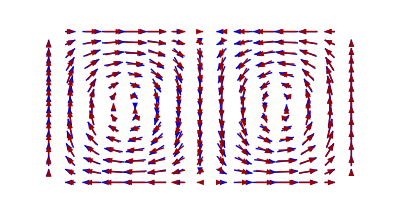

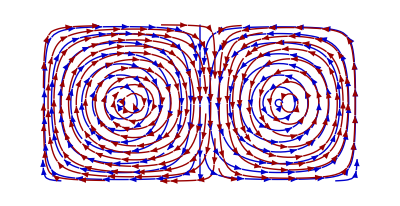

```mathematica
sys0={vx[t,x,y],vy[t,x,y]}/.params/.t->0;
sys1={vx[t,x,y],vy[t,x,y]}/.params/.t->2.5;
vecFig=Show[{
VectorPlot[sys0,{x,0,2},{y,0,1},AspectRatio->Automatic,Axes->False,Frame->False,VectorStyle->Darker[Blue,.2]],
VectorPlot[sys1,{x,0,2},{y,0,1},AspectRatio->Automatic,Axes->False,Frame->False,VectorStyle->Darker[Red,.4]]
}]
streamFig=Show[{
StreamPlot[sys0,{x,0,2},{y,0,1},AspectRatio->Automatic,Axes->False,Frame->False,StreamStyle->Darker[Blue,.2]],
StreamPlot[sys1,{x,0,2},{y,0,1},AspectRatio->Automatic,Axes->False,Frame->False,StreamStyle->Darker[Red,.4]]
}]

(*
Export["vecFig.png",vecFig,ImageResolution->300];
Export["streamFig.png",streamFig,ImageResolution->300];
*)
```

## Demonstrations of functions

### Plot pathlines

```mathematica
?pathPlot
```

Given velocity field data, generate a series of equal-time trajectories from uniform 
initial conditions

Arguments:
xlo: Real
	The lower bound on x
xhi: Real
	The upper bound on x
ylo: Real
	The lower bound on y
yhi: Real
	The upper bound on y
tlo: Real
	The starting value for t
thi: Real
	The ending value for t

Arguments (Optional):
n : Integer
	The number of points to use to discretize the domain 
seeds1 : List of {Real, Real}
	An explicit list of starting points to use for the integration
Options[ParametricPlot] : Any plotting options that would normally be passed to ParametricPlot

Plot pathlines of a flow and modify the plot properties

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

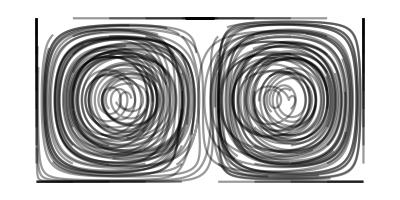

```mathematica
pathFig=pathPlot[{vx[t,x,y],vy[t,x,y]}/.params,{x,0,2},{y,0,1},{t,0,15},PlotStyle->{{Black,Opacity[.4]}},Axes->False]
(*Export["pathFig.png",pathFig,ImageResolution->300]*)
```

Specify the resolution of the streamline plotting

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

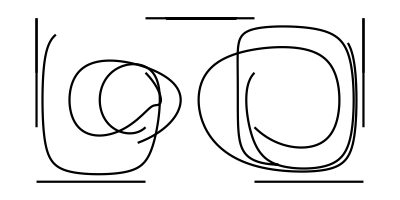

```mathematica
pathPlot[
{vx[t,x,y],vy[t,x,y]}/.params,
{x,0,2},
{y,0,1},
{t,0,15},
{n->20},
PlotStyle->Black,
Axes->False]
```

Pass an explicit list of starting points

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

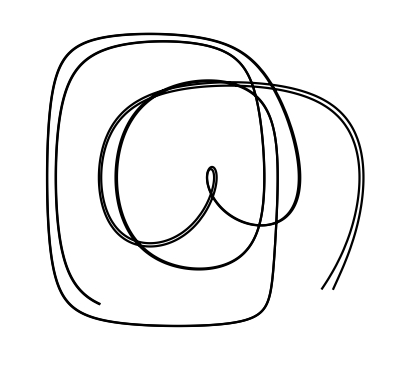

```mathematica
pathPlot[
{vx[t,x,y],vy[t,x,y]}/.params,
{x,0,2},{y,0,1},{t,0,45},
{seeds1->{{.2,.1}, {.201,.101}}},
PlotStyle->Black,Axes->False
]
```

### Visualize advection of a blob

```mathematica
?advectPoints
```

Given a collection of initial conditions, advect them forward in time

Arguments:
seedPoints : N-ist of 2-Lists;
	A list of starting points at which to initialize trajectories

vfield : Pair of functions in x,y;
	Cartesian expression of a 2D vector field

timeLimit : Real;
	The amount of time to integrate

```mathematica
blobPoints=makeMesh[{.2,.6},{.1,.5},50,50];
ptLocs=advectPoints[ 
blobPoints,
{vx[t,x,y],vy[t,x,y]}/.params,
{t,0,20},x,y];
im=Show[{
ListPlot[Flatten[{x[t],y[t]}/.ptLocs/.t->1,1],PlotStyle->Lighter[Blue,.9],PlotMarkers->{Automatic,3}],
ListPlot[Flatten[{x[t],y[t]}/.ptLocs/.t->5,1],PlotStyle->Lighter[Blue,.6],PlotMarkers->{Automatic,3}],
ListPlot[Flatten[{x[t],y[t]}/.ptLocs/.t->20,1],PlotStyle->Blue,PlotMarkers->{Automatic,3}]
},
PlotRange->{{0,2},{0,1}},AspectRatio->Automatic,Axes->False];
transportFig=ImageReflect[ImageReflect[Image[im],Top],Left]

(*Export["transportFig.png",im,ImageResolution->300]*)
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

-Graphics-

### Visualize the final locations of particles

```mathematica
blobPoints=makeMesh[{0,2},{0,1},300,300];
tLim=50;
(* 3 GB *)
ptLocs=advectPointsFinal[ 
blobPoints,
{vx[t,x,y],vy[t,x,y]}/.params,
{t,0,tLim},x,y];
finalLocs=Transpose[Join[Transpose[blobPoints],{Transpose[ptLocs]⟦1⟧-1}]];
```

NDSolveValue::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

```mathematica
ListDensityPlot[
finalLocs,
InterpolationOrder->3,
ColorFunction->"ThermometerColors",
AspectRatio->Automatic,
Axes->False,
Frame->False
]
```

-Graphics-

### Visualize the field of maximal Lyapunov exponents

```mathematica
?findMaxFTLEField
```

Given a velocity field and a set of coordinate points, compute the max FTLE field 
at a given timepoint

Arguments:
vfield : Pair of functions in x,y
	Cartesian expression of a 2D vector field
seeds : N-ist of 2-Lists
	A list of starting points at which to initialize trajectories
tlo : Real
	The time to start integration
thi : Real
	The time to stop integration

Returns:
ftleField : List of 3-Lists 
	A list of {x,y,lambda} points denoting the max finite time
	Lyapunov exponents at each location

NDSolveValue::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

ReplaceAll::reps: {allTraj$340444} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

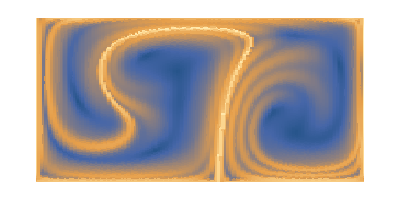

```mathematica
params =  {A->0.1,ϵ->0.25,ω->π/5};
domainPoints=makeMesh[{0,2},{0,1},150,150];
ftleField=findMaxFTLEField[{vx[t,x,y],vy[t,x,y]}/.params,domainPoints,{t,0,10},x,y];
ftlePlot=ListDensityPlot[ftleField,InterpolationOrder->0,AspectRatio->Automatic,Axes->False,Frame->False]
(*Export["ftlePlot.png",ftlePlot,ImageResolution->300]*)
```

### Visualize the Kaplan-Yorke exponents

```mathematica
?findFTLEField
?findKYDim
```

Given a velocity field and a set of coordinate points, compute the FTLE field 
at a given timepoint

Arguments:
vfield : Pair of functions in x,y
	Cartesian expression of a 2D vector field
seeds : N-ist of 2-Lists
	A list of starting points at which to initialize trajectories
tlo : Real
	The time to start integration
thi : Real
	The time to stop integration

Returns:
ftleField : List of 3-Lists 
	A list of {x,y,{lamba1,lambda2} points denoting the two finite time
	Lyapunov exponents at each location

Given a list of Lyapunov exponents, compute the Kaplan-Yorke fractal dimension

Arguments:
ptList : A List of {x,y,{lamba1,lambda2}} points denoting the two Lyapunov 
	exponents at each location


Returns:
kyField : List of 3-Lists 
	A list of {x,y,K} points denoting the Kaplan-Yorke dimension at
	each location

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

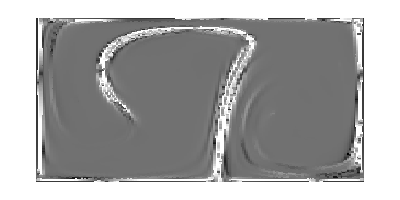

kyfig.png

```mathematica
domainPoints=makeMesh[{0,2},{0,1},150,150];
ftleVals=findFTLEField[{vx[t,x,y],vy[t,x,y]}/.params,domainPoints,{t,0,10},x,y];
kyVals=findKYDim[ftleVals];

signedLog=Sign[#]Log[1+Abs[#]]&; (* for visualization *)
kyfig=ListDensityPlot[{#[[1]],#[[2]],signedLog[#[[3]]]}&/@kyVals,InterpolationOrder->0,AspectRatio->Automatic,PlotRange->{Automatic,1.5},ColorFunction->GrayLevel,Axes->False,Frame->False]
(*Export["kyfig.png",kyfig,ImageResolution->300]*)
```

### Draw lines of maximal stretching

```mathematica
?findStretchlines
```

Given a velocity field and a set of coordinate points, compute the vector field 
corresponding to the maximum or minimum stretching direction

Arguments:
vfield : Pair of functions in x,y
	Cartesian expression of a 2D vector field
seeds : N-ist of 2-Lists
	A list of starting points at which to initialize trajectories
tlo : Real
	The time to start integration
thi : Real
	The time to stop integration
ordering : String
	Whether to compute the field for maximum or minimum streching

Returns:
stretchField : List of 3-Lists 
	A list of {x,y,{v1, v2}} points denoting the stretching field
	at each location

Compute the vector fields associated with maximum and minimal stretching at each location, and overlay them in different colors

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

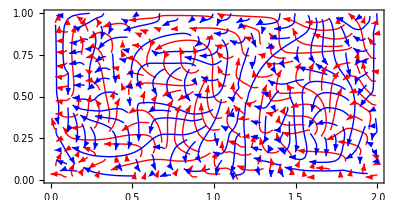

```mathematica
blobPoints=makeMesh[{0,2},{0,1},100,100];
stretchVecsPositive=findStretchlines[{vx[t,x,y],vy[t,x,y]}/.params,blobPoints,{t,0,10},x,y,"Positive"];
stretchVecsNegative=findStretchlines[{vx[t,x,y],vy[t,x,y]}/.params,blobPoints,{t,0,10},x,y,"Negative"];

Show[{
ListStreamPlot[{{#[[1]],#[[2]]},#[[3]]}&/@stretchVecsPositive,AspectRatio->Automatic,PlotRange->All,StreamStyle->Red,StreamScale->{10,500,.005}],
ListStreamPlot[{{#[[1]],#[[2]]},#[[3]]}&/@stretchVecsNegative,AspectRatio->Automatic,PlotRange->All,StreamStyle->Blue,StreamScale->{10,500,.005}]
}]
```

Overlay stretching lines on the FTLE field

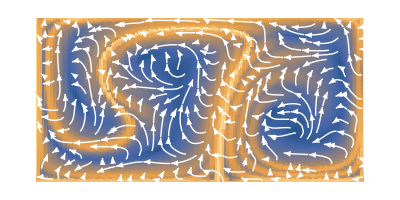

stretchFig.png

```mathematica
stretchFig=Show[
{
ListDensityPlot[ftleField,InterpolationOrder->0,AspectRatio->Automatic],
(*ListVectorPlot[{{#[[1]],#[[2]]},#[[3]]}&/@stretchVecs,AspectRatio->Automatic,PlotRange->All,VectorStyle->White]*)
ListStreamPlot[{{#[[1]],#[[2]]},#[[3]]}&/@stretchVecsPositive,AspectRatio->Automatic,PlotRange->All,StreamStyle->White]
},Frame->False]
(*Export["stretchFig.png",stretchFig,ImageResolution->300]*)
```

### Find flushing times

```mathematica
?flushingTimes
```

Given a velocity field and a domain, calculate the flushing time field

Arguments:
vfield : Pair of functions in x,y,t
	Cartesian expression of a 2D time-dependent vector field
xlo: Real
	The lower bound on x
xhi: Real
	The upper bound on x
ylo: Real
	The lower bound on y
yhi: Real
	The upper bound on y
tlo : Real
	The time to start integration
thi : Real
	The time to stop integration (the maximum flushing time)

Arguments (Optional):
n : Integer
	The number of points to use to discretize the domain 
seeds1 : List of {Real, Real}
	An explicit list of starting points to use for the integration
Options[ParametricPlot] : Any plotting options that would normally be
					      passed to ParametricPlot

Returns:
flushField : List of 3-Lists
	A list of {x,y,t} points denoting the flushing time at 
	each spatial location

```mathematica
flushField=flushingTimes[
{vx[t,x,y],vy[t,x,y]}/.params,
{x,-1,1},
{y,0,1},
{t,0,50},
{n->20000}];
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 37.4931 and t = 37.5576.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 39.8363 and t = 39.9074.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 37.4662 and t = 37.5299.

General::stop: Further output of NDSolve::evcvmit will be suppressed during this calculation.

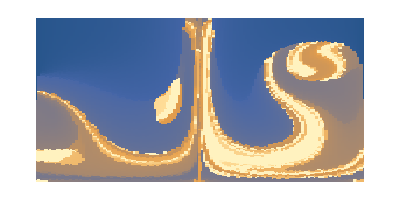

flushFig.png

```mathematica
flushFig=ListDensityPlot[flushField,InterpolationOrder->0,AspectRatio->Automatic,Frame->False]
(*Export["flushFig.png",flushFig,ImageResolution->300]*)
```

### Make video of a time-varying flow

```mathematica
?animateFlow
```

Given a velocity field and a domain, create a video of the flow as it 
evolves in time

Arguments:
vfield : Pair of functions in x,y,t
	Cartesian expression of a 2D time-dependent vector field
seeds : Length N List of 2-Lists
	A list of starting points at which to initialize trajectories
xlo: Real
	The lower bound on x
xhi: Real
	The upper bound on x
ylo: Real
	The lower bound on y
yhi: Real
	The upper bound on y
tlo : Real
	The time to start integration
thi : Real
	The time to stop integration (the maximum flushing time)
frameRate : Integer
	The number of frames per second of the video
playbackSpeed : Integer
	The playback rate, 1x, 2x, etc.
filename : String
	The name of the video. The extension .avi may also be used

Returns: None

```mathematica
blobPoints=makeMesh[{1.2,1.6},{.1,.5},50,50];
animateFlow[ 
{vx[t,x,y],vy[t,x,y]}/.params,
blobPoints,
{t,0,20},
{x,0,2},
{y,0,1},
20,1/10];

(*makeMesh[{1.2,1.6},{.1,.5},50,50],
{vx[t,x,y],vy[t,x,y]}/.params,
{t,0,20},x,y];*)
```

NDSolve::ndinnt: Initial condition x0 is not a number or a rectangular array of numbers.

# Import an experimental velocity field

This section shows how to import an experimental velocity field, and then use it to calculate a maximal FTLE field

#### Import dataset

```mathematica
rawData=Import["resources/bco_dmo_lakedata_729461.mat"]; (* Source: https://www.bco-dmo.org/dataset-deployment/730831 *)

(* Data must have the format (t, x, y, vx, vy) *)
data=rawData[[2;;6]] ;

(* Get bounds of dataset *)
{xMin,xMax}={Min[#],Max[#]}&@data[[3]];
{yMin,yMax}={Min[#],Max[#]}&@data[[4]];

(* Interpolate velocity field functions *)
{vx,vy}=fitVField[data];
```

#### Compute maximal FTLE field

```mathematica
domainPoints=makeMesh[{xMin,.3*xMax},{yMin,.3*yMax},30,30];
ftleField=Quiet@findMaxFTLEField[{vx[t,x,y],vy[t,x,y]},domainPoints,{t,.001,10},x,y]; (* Compute expensive *)
```

$Aborted

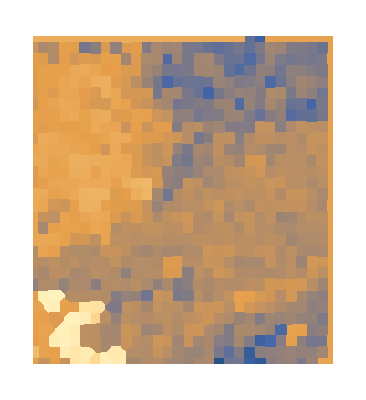

```mathematica
ListDensityPlot[{#[[1]],#[[2]],Log[#[[3]]]}&/@ftleField,
InterpolationOrder->0,
ScalingFunctions->{"Linear","Linear","Log"},
AspectRatio->Automatic,
Axes->False,
Frame->False]
```